```mathematica
Clear[f,df];
f[x_] := Cos[E^x+ 6Sin[x]]
```

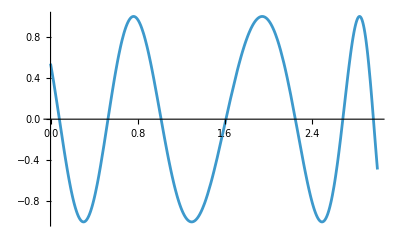

```mathematica
Plot[f[x], {x,0,3}]
```

```mathematica
Clear[f];

f[x_] := x^8 * ArcTan[x];

Integrate[f[x], x]
```

1/216 (12 x^2-6 x^4+4 x^6-3 x^8+24 x^9 ArcTan[x]-12 Log[1+x^2])

```mathematica
12/216
```

1/18

```mathematica
Clear[f];

f[x_] = x^5 Log[2x + 1];
N[f''''''[1]]
```

119.835

```mathematica
Clear[A,a];
A= {{3.1, a, 2.3},{-2.1,2.4,5.6},{1.2,1.1,a}};

Det[A]
```

-31.033+14.16 a+2.1 a^2

```mathematica
Clear[A,B];

A = {{1,2,3},{4,5,6}};
B = {{10,11},{12,13},{14,15}};

MatrixForm[(A.B)^4]
```

(33362176 | 45212176
1146228736 | 1568239201)

```mathematica
Clear[A];

A = {{1,1,1,1,82}, {2,3,4,1,210},{2,1,2,2,185},{5,2,4,5,423}};

RowReduce[A]
```

{{1,0,0,0,20},{0,1,0,0,-21},{0,0,1,0,50},{0,0,0,1,33}}

```mathematica
Clear[A,x,y,z,w];
A = {{1,1,1,1}, {2,3,4,1},{2,1,2,2},{5,2,4,5}};
v = {{x},{y},{z},{w}};
b = {{82},{210},{185},{423}};

Solve[A.v == b, {x,y,z,w}]
```

{{x→20,y→-21,z→50,w→33}}